#### Compute data in x-ω space

```mathematica
<<ThinLayer`
```

```mathematica
BZV=Uncompress@Import[NotebookDirectory[]<>"BesselZeros.mc","String"];
Print["Number of J roots: "<>ToString[Dimensions[BZV][[2]]]];
```

Number of J roots: 30000

```mathematica
computeResponse[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]:=
Module[{zs=.4,zb=.8,D2=1,layers,overburden,model,dList,integrandp,toHTp,HTvec,deltafreq,ωList,toHTk,setlayer,uz,ur,pcrit,UzUr,time,ωI,Nb,test},
(* ==== MODEL PARAMETERS ====*)
overburden=1;
layers={2}~Join~(Sequence@@@ConstantArray[{3,2},Nrep])~Join~{3};
dList={0}~Join~ConstantArray[D2/(Length@layers-1),Length@layers-1]~Join~{0};
model={overburden,Sequence@@layers};

setlayer[]:=Module[
{vp1=2.8,vs1=1,ρ1=1,vp2=3.5,vs2=1.5,ρ2=1.5,vp3=4,vs3=2,ρ3=2},
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,tlCijFromThomsen[vp2,vs2,0.1,0.2,ρ2]];
tlSetLayer[3,tlCijFromThomsen[vp3,vs3,0,0,ρ3]];
];

setlayer[];
pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[DeleteDuplicates@model]];
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
ωI=Log[10.]deltafreq/5;


uz[p_,ω_]:=tlResponse[model,dList,p( ω-I ωI)/√(ω^2+ωI^2),ω+I ωI,zs,zb][[1]];
ur[p_,ω_]:=tlResponse[model,dList,p( ω-I ωI)/√(ω^2+ωI^2),ω+I ωI,zs,zb][[2]];

Nb=Dimensions[BV][[2]];

Module[{BesselTakeUpToN,pmax,rmax},
BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],Round[Nb/3]},{ωList[[-1]],Nb}},InterpolationOrder->1][w]];

pmax[ω_]=2Max@Abs@pcrit;
rmax[ω_]:=BV[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];

DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[uz,ur,pmax,ωList,offsets,setlayer,rmax];

(*===IDHT===*)
time=AbsoluteTiming[
test=ParallelTable[
Module[{BVω=BV[[;;,1;;BesselTakeUpToN[ω]]],u},
setlayer[];
u={
uz[#,ω]&/@(BVω[[1]]/rmax[ω]/ω),ur[#,ω]&/@(BVω[[2]]/rmax[ω]/ω)
};

{Quiet@tlDHTR[u[[1]],0,offsets,rmax[ω],BVω[[1]]],
Quiet@tlDHTR[u[[2]],1,offsets,rmax[ω],BVω[[2]]]}]/ω^2
,{ω,ωList},DistributedContexts->"ThinLayer`Private`"
];
][[1]];

Print["It took me "<>ToString[Round[time/60]]<>" minutes"];
{ωList,test,ωI}
]

]
```

```mathematica
(*computeResponse[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]*)
```

```mathematica
x=Range[.01,2,.01];
```

```mathematica
{freqvec,dataVTItest,ωI}=computeResponse[0,150,50,x,100,BZV[[;;,1;;15000]]];
```

It took me 84 minutes

{-28.8409,100.}

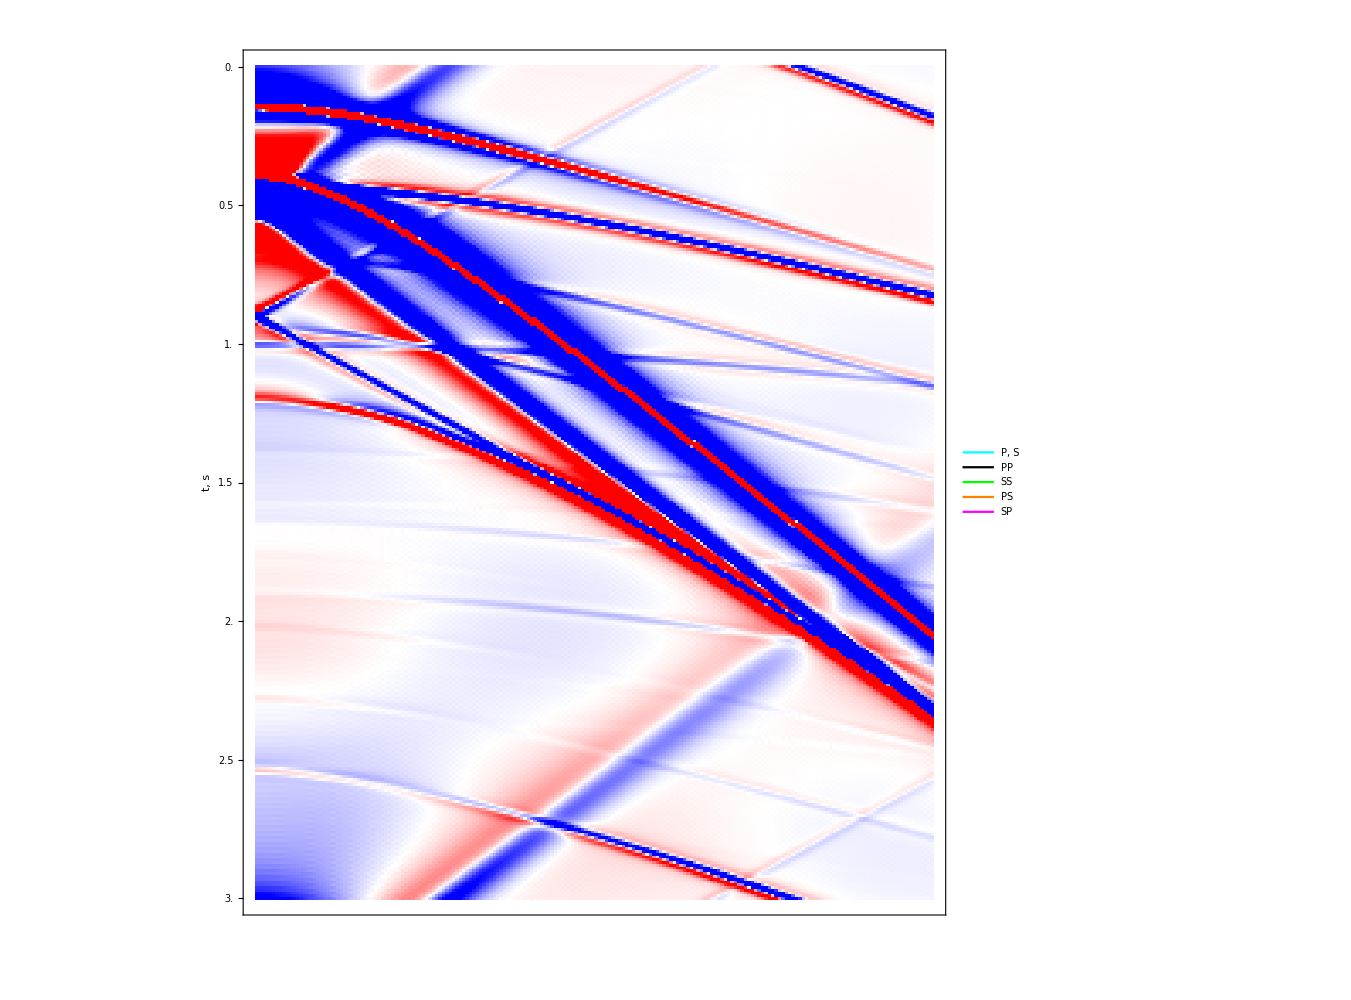
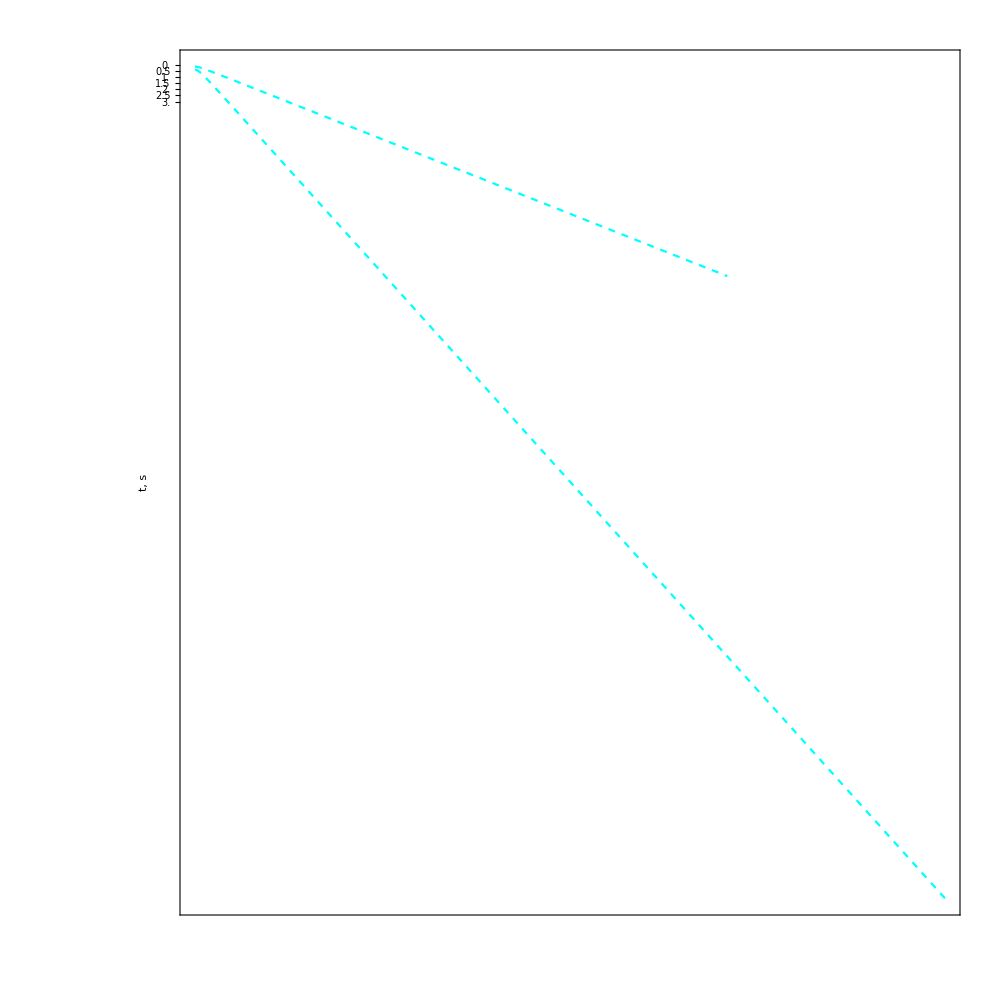
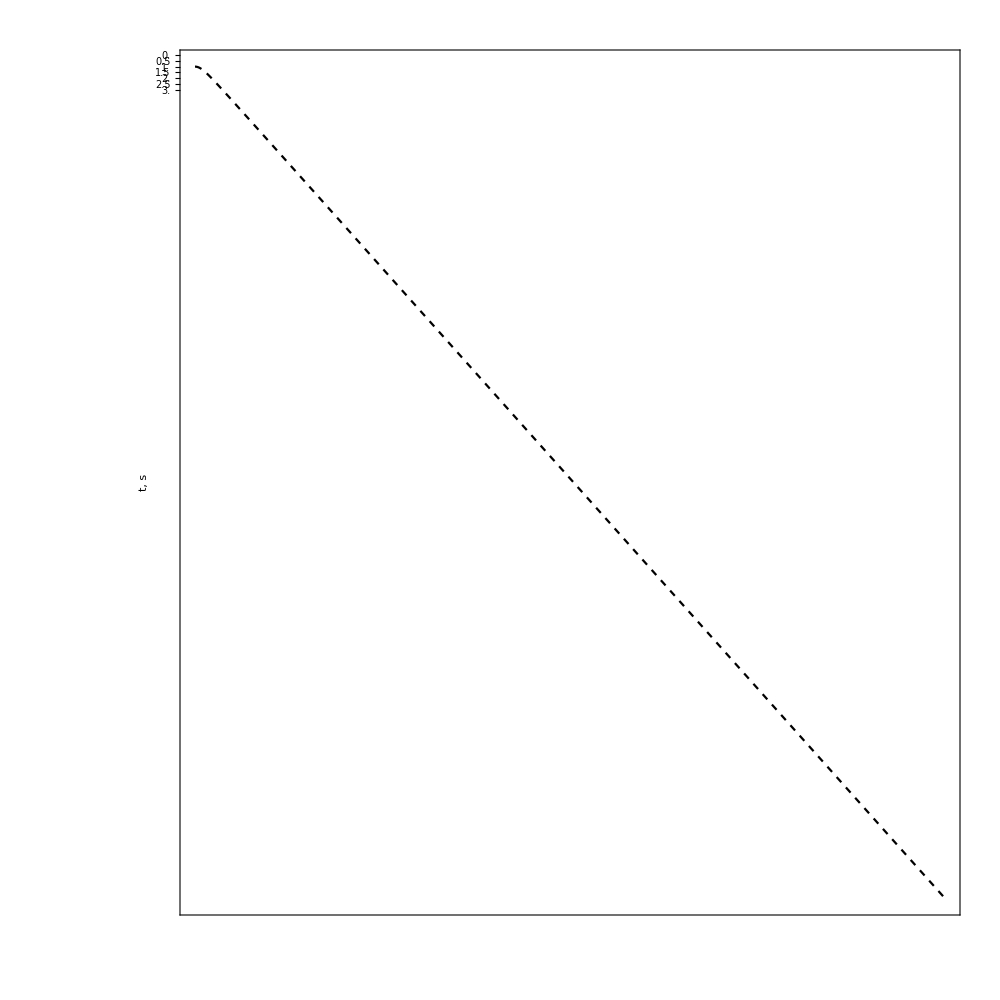
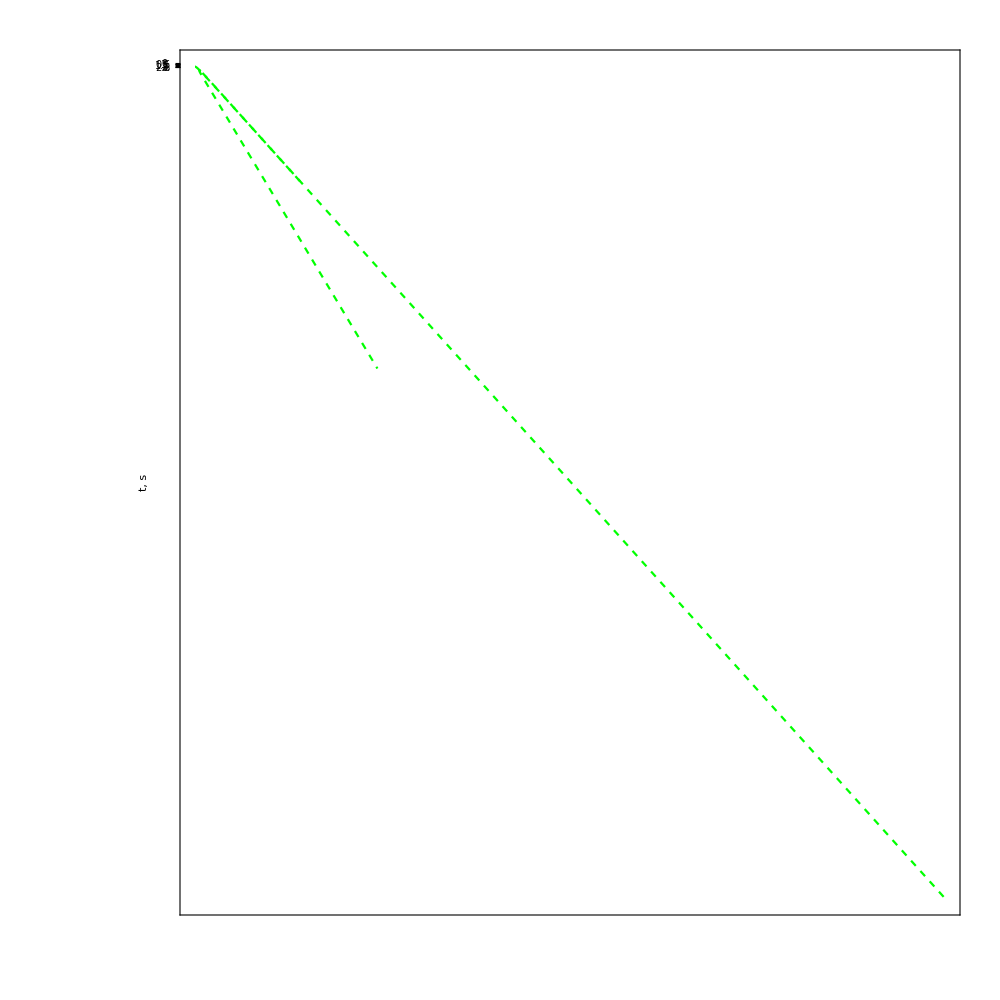
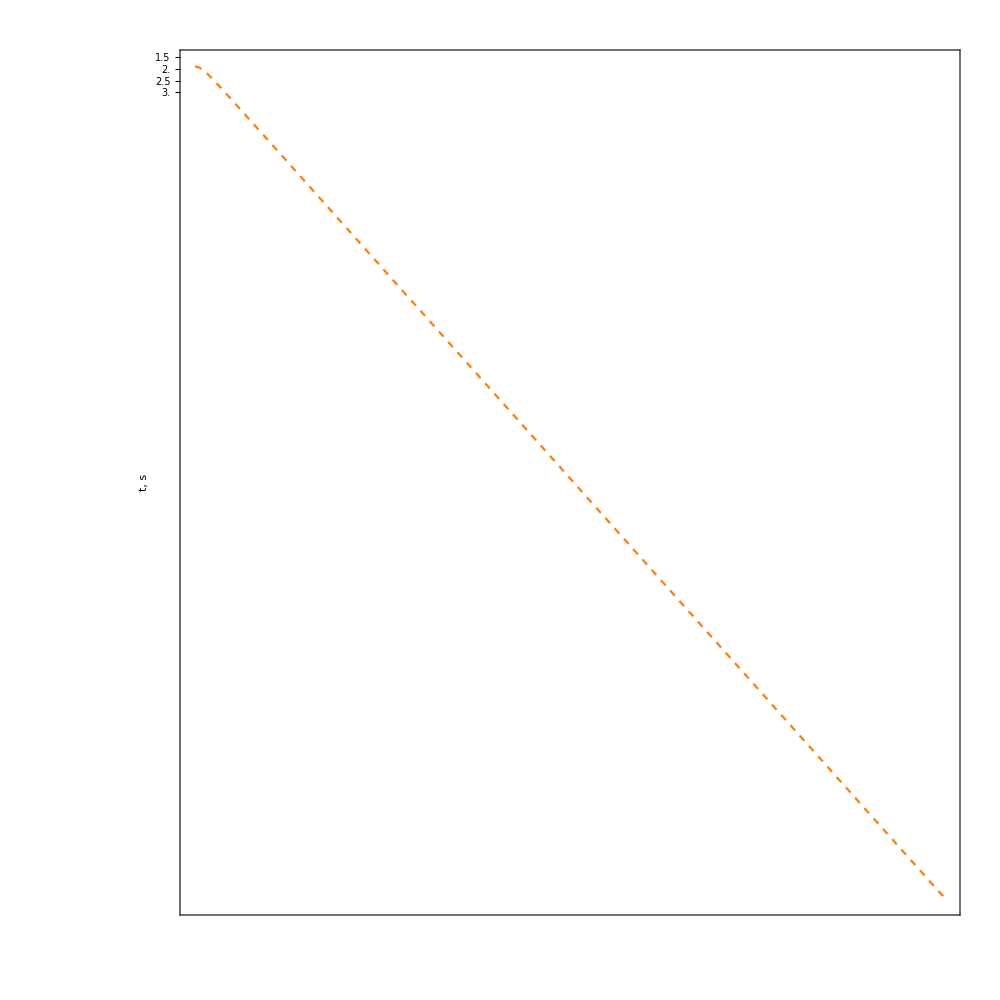
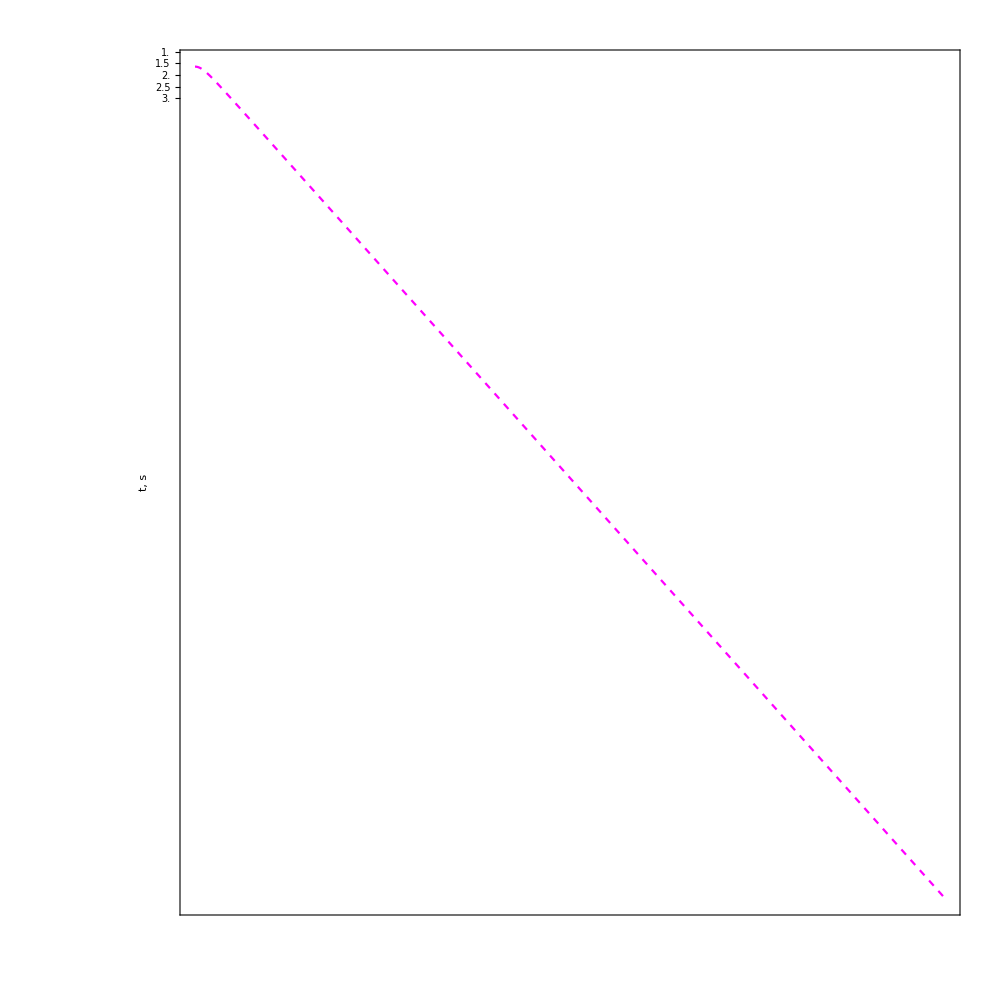

```mathematica
plot[dataVTItest[[;;,1,;;]],freqvec,x,100,ωI]
```